```mathematica
Unprotect[MessageDialog];
MessageDialog=Print;
```

```mathematica
Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/wordLifeDirectory/wordLife.m" ];
```

{generatingFormula time = ,{0.138546,Null}}

variables = 175

sat time = 0.061524

sat time = 0.061524

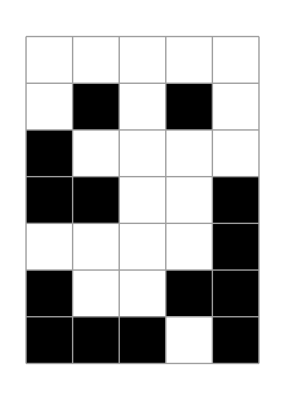

```mathematica
LIFE=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
statePlot[
updateIJ[LIFE]  
]
```

```mathematica
Clear[x4,x3,x2,x1,x0,xp,formulaIJ,i,j];
xpArray=LIFE;
```

```mathematica
Get[NotebookDirectory[]<>"IJ.m"]
```

-Graphics-

```mathematica
and@(Join[Flatten@Array[FORMULA[x4,xp],{i,j}],Flatten@Array[FORMULA[x3,x4],{i,j}],Flatten@Array[FORMULA[x2,x3],{i,j}],Flatten@Array[FORMULA[x1,x2],{i,j}],Flatten@Array[FORMULA[x0,x1],{i,j}]])
```

1
 |  |  |  |

## start

# IJ2-----------------------------------------------------------

```mathematica
Clear[x4,x3,x2,x1,x0,xp,formulaIJ,i,j];
xpArray=LIFE;
```

```mathematica
Get[NotebookDirectory[]<>"IJ2.m"]
```

Set::shape: Lists {xp[1,1,1],xp[1,1,2],xp[1,1,3],xp[1,1,4],xp[1,1,5],xp[1,1,6]} and False are not the same shape.

Set::shape: Lists {xp[1,2,1],xp[1,2,2],xp[1,2,3],xp[1,2,4],xp[1,2,5],xp[1,2,6]} and False are not the same shape.

Set::shape: Lists {xp[1,3,1],xp[1,3,2],xp[1,3,3],xp[1,3,4],xp[1,3,5],xp[1,3,6]} and False are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

ArrayPlot::mat: Argument unsatisfiable at position 1 is not a list of lists.

ArrayPlot[unsatisfiable,Frame→False,Mesh→True]

```mathematica
Array[S,{5,7,6}]//CopyToClipboard
```

# >>-----------------------------------------------------------